# Starobinsky Potential

# This notebook is a part of my Diploma Thesis with title “Swampland Conjectures and Constraints on Inflation” . The knowledge of the theoretical results is important, if someone wishes to follow the presented results in this notebook. My Thesis can be found in an other file in my GitHub repository.

## Definition of the Potential and Introduction of the Slow-Roll parameters

## In this section we will introduce the potential and the slow-roll parameters

```mathematica
v[x_]:=Λ^4*(1-Exp[-√(2/3)k*x])^2
ε1=a/(2*k^2)*(v'[x]/v[x])^2// Simplify;
ε2=-a/k^2*(v''[x]/v[x])+ε1// Simplify;
ε=ε1/a// Simplify;
η=1/k^2*(v''[x]/v[x])// Simplify;
η1=a*η// Simplify;
```

It is required by the theory that the period of inflation should stop when the flatness conditions are a not satisfied, so when ε1=1

```mathematica
Solve[ε1==1,x]
```

{{x→ConditionalExpression[(√(3/2) (2 ⅈ π C[1]+Log[1/3 (3-2 √3 √a)]))/k, C[1]∈ℤ]},{x→ConditionalExpression[(√(3/2) (2 ⅈ π C[1]+Log[1/3 (3+2 √3 √a)]))/k, C[1]∈ℤ]}}

We have to choose second possible solution, so we set with xf the final value for the φ.

```mathematica
xf=(√(3/2) (Log[1/3 (3+2 √3 √a)]))/k//Simplify
```

(√(3/2) Log[1+(2 √a)/(√3)])/k

We proceed to the calculation of the initial value of φ , which denoted as xi
Firstly, the integral for the e-folding number is calculated.

```mathematica
Integrate[-(k^2/a)*(v[x]/v'[x]),x]// Simplify;
```

```mathematica
Solve[(-3 ⅇ^(√(2/3) k xf))/(4 a)-(-3 ⅇ^(√(2/3) k x))/(4 a)==Y,x]
```

{{x→ConditionalExpression[(√(3/2) (2 ⅈ π C[1]+Log[1/3 (3+2 √3 √a+4 a Y)]))/k, C[1]∈ℤ]}}

```mathematica
xi=(√(3/2) (Log[1/3 (3+2 √3 √a+4 a Y)]))/k// Simplify;
```

# Calculation of the observational indices

We calculate the slow-roll parameters for
φ = φi and we take the Taylor approximation for N → ∞. Afterwards, we
calculate the primordial density perturbation and the tensor to scalar ratio for φ = φi and we start our primary work.

```mathematica
ε1i=ε1 /. x->xi// Simplify;
ε2i=ε2 /. x->xi// Simplify;
εi=ε /. x->xi// Simplify;
η1i=η1 /. x->xi// Simplify;
ηi=η/. x->xi// Simplify;
```

Taylor approximation for N → ∞

```mathematica
Series[ε1i,{Y,Infinity,2}];
Series[ε2i,{Y,Infinity,2}];
Series[εi,{Y,Infinity,2}];
Series[η1i,{Y,Infinity,2}];
Series[ηi,{Y,Infinity,2}];
```

```mathematica
ε1i=3/(4 a Y^2)//Simplify;
ε2i=1/Y-(√3)/(2 √a Y^2)// Simplify;
εi=3/(4 a^2 Y^2)// Simplify;
η1i=-1/Y+(3+2 √3 √a)/(4 a Y^2)// Simplify;
ηi=-1/(a Y)+(3+2 √3 √a)/(4 a^2 Y^2)// Simplify;
```

The primordial density perturbation and the tensor to scalar ratio is given as:

```mathematica
ns=1-6*ε1i+2*η1i//Simplify;
r=16*ε1i//Simplify;
```

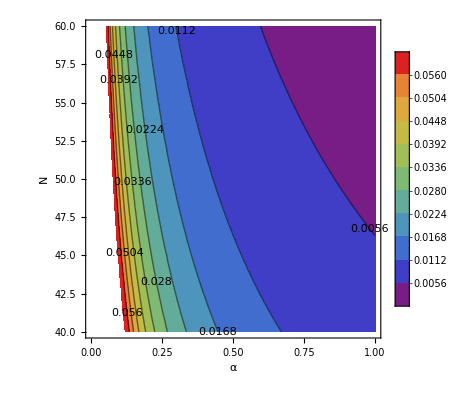

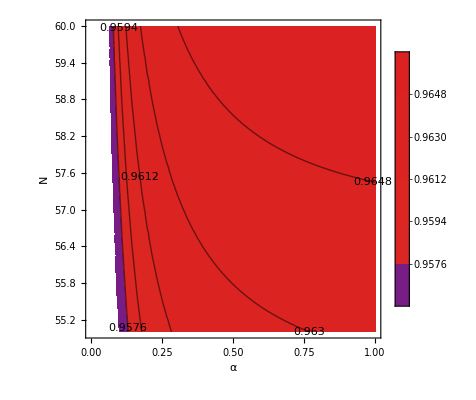

```mathematica
ContourPlot[r,{a,0,1},{Y,40,60},FrameLabel->{α,N},PlotLegends->Automatic, ContourLabels->True,ColorFunction->"Rainbow",Contours->10]
ContourPlot[(-3+√3 √a+a (-2+Y) Y)/(a Y^2),{a,0,1},{Y,55,60},FrameLabel->{α,N},PlotLegends->Automatic, ContourLabels->True,ColorFunction->"Rainbow",Contours->5]
```

At this point we will set N=60 and proceed to extract the constraints. Firstly, we have the primordial density perturbation

```mathematica
(-3+√3 √a+a (-2+Y) Y)/(a Y^2)/. Y->60// Simplify;
ns60=(-3+√3 √a+3480 a)/(3600 a)// Simplify;
Reduce[{ns60>0.9607&& ns60<0.9691},a]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

a>0.112606

Then we have the tensor to scalar ratio.

```mathematica
r60=r/. Y->60// Simplify;
Reduce[r60<0.056,a]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

a<0||a>0.0595238

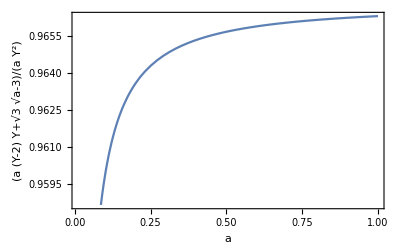

```mathematica
Plot[ns60,{a,0.0109565,1},Frame->True,FrameLabel->{a,ns}]
```

```mathematica
nsmax=(-3+√3 √a+3480 a)/(3600 a)/. a->1// N
```

0.966314

```mathematica
nsmin=(-3+√3 √a+3480 a)/(3600 a)/. a->0.0109565// N
```

0.895205

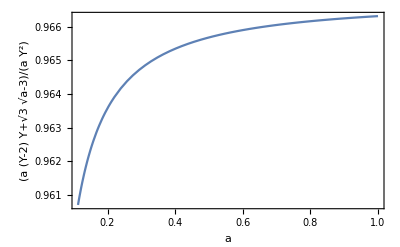

```mathematica
Plot[ns60,{a,0.112606,1},Frame->True,FrameLabel->{a,ns}]
```

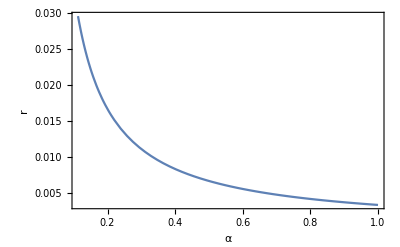

```mathematica
Plot[1/(300 a),{a,0.112606,1},Frame->True,FrameLabel->{α,"r"}]
```

Slow- Roll parameters for N=60

```mathematica
ε1i60=ε1i/. Y->60;
ε2i60=ε2i/. Y->60;
εi60=εi/. Y->60;
η1i60=η1i/. Y->60;
ηi60=ηi/. Y->60;
```

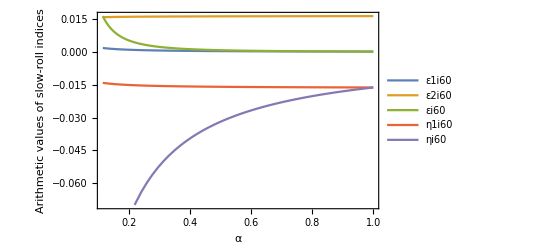

```mathematica
Plot[{ε1i60,ε2i60,εi60,η1i60,ηi60},{a,0.112606,1},Frame->True,FrameLabel->{α,"Arithmetic values of slow-roll indices"},PlotLegends->"Expressions"]
```

## Swampland Conjectures

• The Swampland Distance Conjecture limits the validity of an E.F.T.
and set an upper limit for the traversable by the scalar field as following

                                  ∆φ ≤ f ∼ O(1), in natural units

• The De Sitter Conjecture. It declares that it is impossible to create
De Sitter vacua in string theory. This leads us to set of a lower limit
for the gradient of scalar potentials [Tri20]:
V’/V≥ g ∼ O(1). 
• Another important result is the following -V”/V≥ g ∼ O(1).

```mathematica
s=v'[x]/v[x]// Simplify;
sinitial=s/. x->xi// Simplify;
sinitialk=sinitial/. k->1// Simplify
```

(√6)/(√3 √a+2 a Y)

```mathematica
Reduce[(√6)/(√3 √a+2 a *60)>1,a]//N
```

0.<a<0.0184518